```mathematica
Tarea3;

f[x_]:=x^2-Cos[x];
```

```mathematica
NewtonRhapsonStep[x_]:=x-f[x]/f'[x];
NewtonRhapsonStep[0.2]
```

1.77026

```mathematica
NewtonRhapson[x0_,n_]:=Block[{soluciones = {x0},x = x0},
Do[
x = NewtonRhapsonStep[x];
AppendTo[soluciones,x]; (* Añado el nuevo x a la lista *)
,
n (* Número de repeticiones *)
];

soluciones
];
```

```mathematica
listaDeSoluciones = NewtonRhapson[0.2,10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

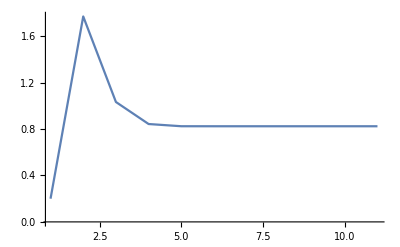

```mathematica
ListLinePlot[listaDeSoluciones,PlotRange->All]
```

```mathematica
Error[x_]:=(-f''[x])/(2f'[x]);
Error[0.2]
```

-2.48891

```mathematica
Error[x0_,n_]:=Block[{errores = {x0},x = x0},
Do[
x = Error[x];
AppendTo[errores,x]; 
,
n
];

errores
];
```

```mathematica
listaDeError = Error[0.2,10]
```

{0.2,-2.48891,0.107924,-4.62689,0.115932,-4.30643,0.104307,-4.78776,0.120961,-4.12683,0.0975261}

```mathematica
Map[Error,{0.2,1.7702601243875122,1.033212831100177,0.8433339058427878,0.8243345563998916,0.8241323352972675,0.8241323123025227,0.8241323123025224,0.8241323123025224,0.8241323123025224,0.8241323123025224}]
```

{-2.48891,-0.19929,-0.429357,-0.547553,-0.562172,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331}

```mathematica
ListaDeErrores=Map[Error,{0.2,1.7702601243875122,1.033212831100177,0.8433339058427878,0.8243345563998916,0.8241323352972675,0.8241323123025227,0.8241323123025224,0.8241323123025224,0.8241323123025224,0.8241323123025224}]
```

{-2.48891,-0.19929,-0.429357,-0.547553,-0.562172,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331}

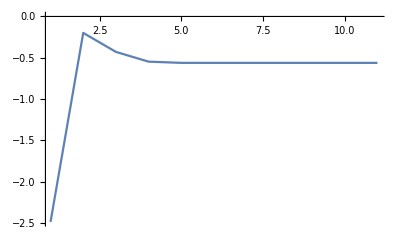

```mathematica
ListLinePlot[ListaDeErrores,PlotRange->All]
```